```mathematica
w = 0.5;   (* define the parameters of Qin interaction *)
d = (0.82)^3/w;
Lam = 0.234;
t = E^2 - 1;
gam = 12.0/25;
mt = 0.5;
```

```mathematica
(* define Qin interaction function *)
```

```mathematica
G[s_]:= ((8*Pi^2*d)/(w^4))E^(-s/w^2) + (8*Pi^2*gam)*((1-E^(-s/(4*mt^2)))/s)/(Log[t+(1+s/Lam^2)^2]);
```

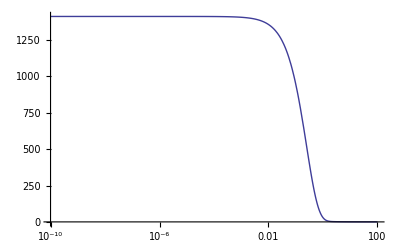

```mathematica
LogLinearPlot[G[x],{x,10^(-10),100}]
```

```mathematica
(* I know how to use FindFit function, but I think this requires a table of values *)
a = Table[{x,G[x]},{x,10^(-20),1000,1}];
```

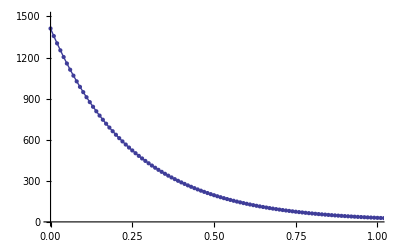

```mathematica
Show[ListPlot[a,PlotRange->{{0,1},{0,1500}}],Plot[G[x],{x,0,1}]]
```

```mathematica
(* find fit for this table *)
FindFit[a,c*(((z1+I*z2)/(x+(mr + I*m)^2))+((z1-I*z2)/(x+(mr-I*m)^2))+((z3+I*z4)/(x+(mr1 + I*m1)^2))+((z3-I*z4)/(x+(mr1-I*m1)^2))),{c,z1,z2,mr,m,z3,z4,mr1,m1},x,Method->NMinimize,PrecisionGoal->  1000,AccuracyGoal->Infinity,MaxIterations->200]
```

{c→-0.823517,z1→-6.74544,z2→-0.569536,mr→0.000822149,m→0.847507,z3→6.00245,z4→-6.72815,mr1→-0.0173023,m1→-0.0950832}

```mathematica
(* below is plotted the new fit, the functional form of the qin interaction, and the old fit; the new fit and the qin interaction are overlapping; the old fit is different as k^2->0 *)
```

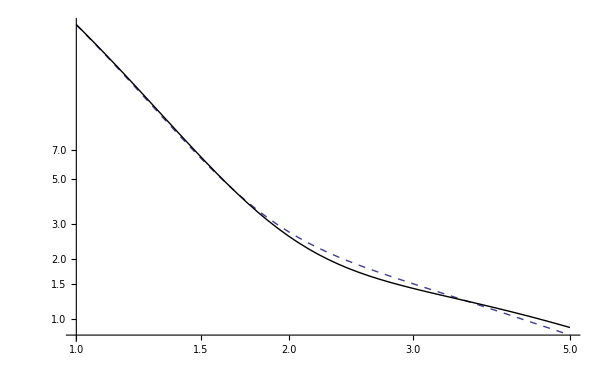

```mathematica
Show[LogLogPlot[G[x],{x,1,5},PlotStyle->Dashed],LogLogPlot[c ((z1+ⅈ z2)/(x+(mr+ⅈ m)^2)+(z1-ⅈ z2)/(x+(mr-ⅈ m)^2)+(z3+ⅈ z4)/(x+(mr1+ⅈ m1)^2)+(z3-ⅈ z4)/(x+(mr1-ⅈ m1)^2))/.{c->5.62877,z1->-7.02346,z2->-17.3725,mr->0.5816931938772835,m->0.7257965328191001,z3->7.14243,z4->78.9026,mr1->0.59545,m1->0.230257115099194},{x,1,5},PlotStyle->Black]]
```

```mathematica
(* below i fit the chiral quark props *)
```

```mathematica
b5 = SetPrecision[Import["Documents/programs1/sig_v_Q2.dat"],50];
p1 = Table[b5[[i,1]],{i,200}];
```

```mathematica
wts = Join[p1,p1];
```

```mathematica
b1 = Import["Documents/programs/sig_v_Q.dat"];
bsc = Import["Downloads/uab.dat"];
```

```mathematica
a1 =Drop[bsc,None,-1];
```

```mathematica
b1d = Drop[bsc,None,{2,2}];
```

```mathematica
b[[1,1]]
```

1.60261×10^-6

```mathematica
fb1 = Interpolation[b5];
```

```mathematica
v = Table[a1[[i,2]]/(a1[[i,1]]*(a1[[i,2]])^2+(b1d[[i,2]])^2),{i,160}];
```

```mathematica
s = Table[b1d[[i,2]]/(a1[[i,1]]*(a1[[i,2]])^2+(b1d[[i,2]])^2),{i,160}];
```

```mathematica
pts = Table[a1[[i,1]],{i,160}];
```

```mathematica
ssh = Table[{pts[[i]],s[[i]]},{i,1,160}];
```

```mathematica
vsc = Table[{pts[[i]],v[[i]]},{i,1,160}];
```

```mathematica
shi = Interpolation[vsc];
```

```mathematica
sh1 = Interpolation[ssh];
```

```mathematica
(z1+ⅈ z2)/(x+(mr+ⅈ m)^2)+(z1-ⅈ z2)/(x+(mr-ⅈ m)^2)+(z3+ⅈ z4)/(x+(mr1+ⅈ m1)^2)+(z3-ⅈ z4)/(x+(mr1-ⅈ m1)^2)/.{z1->0.12060661767968187638326723904974354136`20.,z2->0.11220425731888587228199880123268635556`20.,mr->-1.34187420292095771212359481111675166346`20.,m->-0.91980175971014059765983005537261904797`20.,z3->0.36777178015858792975838295939926420117`20.,z4->0.31621717259369242372562140031739056308`20.,mr1->0.54698766164048715130146495149336056462`20.,m1->0.30652950619098324787517187721005912725`20.}}
```

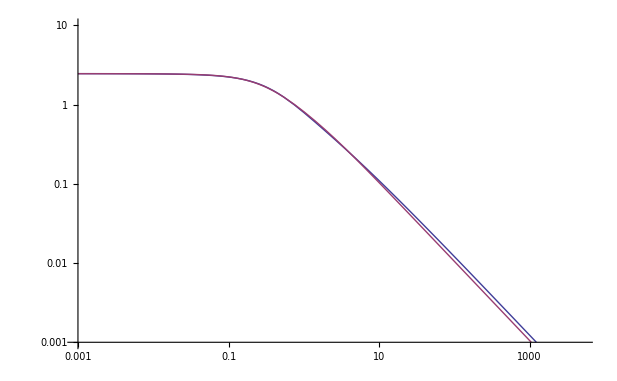

```mathematica
LogLogPlot[{fb1[x],(z1+ⅈ z2)/(x+(mr+ⅈ m)^2)+(z1-ⅈ z2)/(x+(mr-ⅈ m)^2)+(z3+ⅈ z4)/(x+(mr1+ⅈ m1)^2)+(z3-ⅈ z4)/(x+(mr1-ⅈ m1)^2)/.{{z1->0.38407934,z2->-0.24458148,mr->0.52347144,m->-0.27995226,z3->0.14200831,z4->0.02103834,mr1->-1.00400838,m1->-0.69404506}}},{x,0.001,5000},PlotRange->{0.001,10}]
```

```mathematica
bbb= SetPrecision[Import["Documents/programs1/sig_s_Q2.dat"],50];
```

```mathematica
f1 = Interpolation[bbb];
```

```mathematica
0.38407934,-0.24458148,0.52347144,-0.27995226,0.14200831,0.02103834,-1.00400838,-0.69404506
```

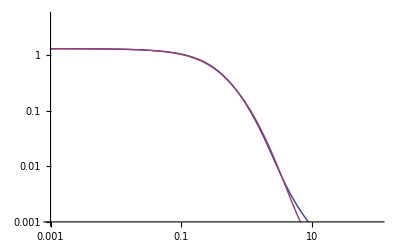

```mathematica
LogLogPlot[{f1[x],(((z1+ⅈ z2)*(mr+ⅈ m))/(x+(mr+ⅈ m)^2)+((z1-ⅈ z2)*(mr-ⅈ m))/(x+(mr-ⅈ m)^2)+((z3+ⅈ z4)*(mr1+ⅈ m1))/(x+(mr1+ⅈ m1)^2)+((z3-ⅈ z4)*(mr1-ⅈ m1))/(x+(mr1-ⅈ m1)^2)) /. {z1->0.38407934,z2->-0.24458148,mr->0.52347144,m->-0.27995226,z3->0.14200831,z4->0.02103834,mr1->-1.00400838,m1->-0.69404506}},{x,0.001,100},PlotRange->{0.001,5}]
```

```mathematica
sigv[x_] := (z1+ⅈ z2)/(x+(mr+ⅈ m)^2)+(z1-ⅈ z2)/(x+(mr-ⅈ m)^2)+(z3+ⅈ z4)/(x+(mr1+ⅈ m1)^2)+(z3-ⅈ z4)/(x+(mr1-ⅈ m1)^2);
```

```mathematica
sigs[x_]:= ((z1+ⅈ z2)*(mr+ⅈ m))/(x+(mr+ⅈ m)^2)+((z1-ⅈ z2)*(mr-ⅈ m))/(x+(mr-ⅈ m)^2)+((z3+ⅈ z4)*(mr1+ⅈ m1))/(x+(mr1+ⅈ m1)^2)+((z3-ⅈ z4)*(mr1-ⅈ m1))/(x+(mr1-ⅈ m1)^2);
```

```mathematica
alldata = Join[{1,Sequence @@ #} & /@ b5, {2, Sequence @@ #} & /@ bbb];
```

```mathematica
myF[index_,x_]:= KroneckerDelta[index-1]*sigv[x]+KroneckerDelta[index-2]*sigs[x];
```

```mathematica
nlm1 = NonlinearModelFit[alldata,{myF[index,x],Re[((z1+ⅈ z2)*(mr+ⅈ m))/(1+(mr+ⅈ m)^2)+((z1-ⅈ z2)*(mr-ⅈ m))/(1+(mr-ⅈ m)^2)+((z3+ⅈ z4)*(mr1+ⅈ m1))/(1+(mr1+ⅈ m1)^2)+((z3-ⅈ z4)*(mr1-ⅈ m1))/(1+(mr1-ⅈ m1)^2)]==f1[1],Re[((z1+ⅈ z2)*(mr+ⅈ m))/(3+(mr+ⅈ m)^2)+((z1-ⅈ z2)*(mr-ⅈ m))/(3+(mr-ⅈ m)^2)+((z3+ⅈ z4)*(mr1+ⅈ m1))/(3+(mr1+ⅈ m1)^2)+((z3-ⅈ z4)*(mr1-ⅈ m1))/(3+(mr1-ⅈ m1)^2)]==f1[3],Re[((z1+ⅈ z2)*(mr+ⅈ m))/(4+(mr+ⅈ m)^2)+((z1-ⅈ z2)*(mr-ⅈ m))/(4+(mr-ⅈ m)^2)+((z3+ⅈ z4)*(mr1+ⅈ m1))/(4+(mr1+ⅈ m1)^2)+((z3-ⅈ z4)*(mr1-ⅈ m1))/(4+(mr1-ⅈ m1)^2)]==f1[4],Re[((z1+ⅈ z2)*(mr+ⅈ m))/(5+(mr+ⅈ m)^2)+((z1-ⅈ z2)*(mr-ⅈ m))/(5+(mr-ⅈ m)^2)+((z3+ⅈ z4)*(mr1+ⅈ m1))/(5+(mr1+ⅈ m1)^2)+((z3-ⅈ z4)*(mr1-ⅈ m1))/(5+(mr1-ⅈ m1)^2)]==f1[5],Re[((z1+ⅈ z2)*(mr+ⅈ m))/(6+(mr+ⅈ m)^2)+((z1-ⅈ z2)*(mr-ⅈ m))/(6+(mr-ⅈ m)^2)+((z3+ⅈ z4)*(mr1+ⅈ m1))/(6+(mr1+ⅈ m1)^2)+((z3-ⅈ z4)*(mr1-ⅈ m1))/(6+(mr1-ⅈ m1)^2)]==f1[6],Re[((z1+ⅈ z2)*(mr+ⅈ m))/(10+(mr+ⅈ m)^2)+((z1-ⅈ z2)*(mr-ⅈ m))/(10+(mr-ⅈ m)^2)+((z3+ⅈ z4)*(mr1+ⅈ m1))/(10+(mr1+ⅈ m1)^2)+((z3-ⅈ z4)*(mr1-ⅈ m1))/(10+(mr1-ⅈ m1)^2)]==f1[10],Re[((z1+ⅈ z2)*(mr+ⅈ m))/(100+(mr+ⅈ m)^2)+((z1-ⅈ z2)*(mr-ⅈ m))/(100+(mr-ⅈ m)^2)+((z3+ⅈ z4)*(mr1+ⅈ m1))/(100+(mr1+ⅈ m1)^2)+((z3-ⅈ z4)*(mr1-ⅈ m1))/(100+(mr1-ⅈ m1)^2)]==f1[100],fb1[100]==(z1+ⅈ z2)/(100+(mr+ⅈ m)^2)+(z1-ⅈ z2)/(100+(mr-ⅈ m)^2)+(z3+ⅈ z4)/(100+(mr1+ⅈ m1)^2)+(z3-ⅈ z4)/(100+(mr1-ⅈ m1)^2)},{{z1,0.1206173690432031},{z2,0.36924937451987244},{mr,0.522023273645157},{m,0.3253893412012962},{z3,-0.02226429458971485},{z4,0},{mr1,0.785367101181189},{m1,1.1857166877984684}},{index,x},Method->NMinimize,PrecisionGoal->  10000000,AccuracyGoal->Infinity,MaxIterations->300]
```

FittedModel[(-(2.05868+0.186289 ⅈ)/((-1371.43-212.202 ⅈ)+x)-(«1»)/(«1»)+«1»+(«1»)/(«1»)) «1»+«1»]

```mathematica
%30["BestFitParameters"]
```

{z1→-2.05868,z2→0.186289,mr→2.85657,m→37.1428,z3→0.44313,z4→0.247468,mr1→0.234305,m1→0.452813}

```mathematica
{z1->0.3248083172691378,z2->-0.3601865275785603,mr->0.54500831654829,m->-0.3193882860651518,z3->0.08417912180069137,z4->0.03475248524804984,mr1->-0.992362926631562,m1->-0.6857868350268325}
```

```mathematica
{z1->0.26483196650316815,z2->0.36924937451987244,mr->0.522023273645157,m->0.3253893412012962,z3->-0.02226429458971485,z4->-0.0008206173824209502,mr1->0.785367101181189,m1->1.1857166877984684}
```

```mathematica
wt1 = Table[i^2,{i,1,200}];
```

```mathematica
wt2 = Table[i^2,{i,1,200}];
```

```mathematica
wt = Join[wt1,wt2];
```

```mathematica
FourierTransform[G[s],s,x]
```

```mathematica
f[x_]:=FourierTransform[1393.096714091478 ⅇ^(-4. s)+(37.899280900183136 (1-ⅇ^(-1. s)))/(s Log[-1+ⅇ^2+(1+18.262838775659286 s)^2]),s,x]
```

```mathematica
Plot[Re[f[x]],{x,1,10}]
```